```mathematica
SetDirectory["C:\\Users\\Anton\\Dropbox\\Work\\2015-09 Slow cooling rates with Sarah Loewy\\Calculations\\Anim"]
Directory[]
```

C:\Users\Anton\Dropbox\Work\2015-09 Slow cooling rates with Sarah Loewy\Calculations\Anim

C:\Users\Anton\Dropbox\Work\2015-09 Slow cooling rates with Sarah Loewy\Calculations\Anim

```mathematica
f1=Function[mu,1/2+Sqrt[(-((n^2-3)*(m-n)^4*(m+n)^4*mu^4+(2*(2*n^4+m^2-5*n^2))*(m-n)^3*(m+n)^3*mu^3-(2*(m^4*n^4+m^2*n^6-4*m^4*n^2-5*m^2*n^4-3*n^6+2*m^4+3*m^2*n^2+7*n^4-m^2-n^2))*(m-n)^2*(m+n)^2*mu^2-(2*(m-n))*(m+n)*(m^2+n^2)*(2*m^2*n^6+2*m^4*n^2-6*m^2*n^4-2*n^6-m^4+2*m^2*n^2+5*n^4-2*n^2)*mu-(n-1)*(n+1)*(m^2+n^2)^2*(m^2+n^2-2)*(2*m^2*n^2-m^2-n^2))/((3*n^2-1)*(m-n)^2*(m+n)^2*mu^2+2*n^2*(m-n)*(m+n)*(m^2+n^2)*mu+(n-1)*(n+1)*(m^2+n^2)^2))]/((2*(mu-1))*(m+n)*(m-n))];
(*Det = 1*)
f1mustupid[mu_]=Simplify[f1[mu]/.m->(n/Sqrt[2]),{{n>0},{mu>0}}];
f1mu[mu_,nn_]=Simplify[f1mustupid[1-mu]/.n->nn];
```

```mathematica
cof[m_]:=Transpose[Map[Reverse,Minors[Transpose[m],2],{0,1}] Table[(-1)^(i+j),{i,3},{j,3}]]
U={{n/Sqrt[2],0,0},{0,n,0},{0,0,n}};
sq=Function[A,Transpose[A].A];
Frob[m_]:=Sqrt[Tr[sq[m]]];
norm=Function[a,Dot[a,a]^(1/2)];
normal=Function[a,a/norm[a]];
```

```mathematica
Mal1=Function[{A,e},Outer[Times,-2*(A.e-(1/Dot[cof[A].e,cof[A].e])*cof[A].e),e]];
Mal1s=Function[{A,e},-2*(A.e-(1/Dot[cof[A].e,cof[A].e])*cof[A].e)]; (*Shear*)
Mal1n=Function[{A,e},e]; (*Normal*)

Mal2=Function[{A,e},Outer[Times,2*A.e,e-(1/Dot[A.e,A.e])*Transpose[A].A.e]];
Mal2s=Function[{A,e},2*A.e];
Mal2n=Function[{A,e},e-(1/Dot[A.e,A.e])*Transpose[A].A.e];
```

```mathematica
Fmdet1[v_,n_]=Simplify[U+v*Mal1 @@{U,{1/√2,1/√2,0}}+(f1mu[v,n])*Mal1@@{U+v*Mal1@@{U,{1/√2,1/√2,0}},{0,1/√2,-1/√2}}];
LAM[k_,n_]=Simplify[sq[Fmdet1[k,n]]];
```

```mathematica
(*Find admissible Intervals*)
Plot[{f1mu[mu,n],g1[mu,n]},{mu,0,1}]
```

-Graphics-

```mathematica
lambda0[n_]:=N[f1mu[1,n]]
mu0l[n_]:=N[mu/.Solve[f1mu[mu,n]==1,mu]]
mu0r[n_]:=Select[N[mu/.Solve[f1mu[mu,n]==1/2,mu]][[2;;]],Im[#]==0&]
Points1[n_]:=Sort[Flatten[{mu0l[n],mu0r[n]}]]
Int2[n_]:=If[Length[Points1[n]]==3,IntervalUnion[Interval[Points1[n][[1;;2]]],Interval[{Points1[n][[3]],1}]],IntervalUnion[Interval[Points1[n][[1;;2]]],Interval[Points1[n][[3;;4]]],Interval[{Points1[n][[5]],1}]]]
Manipulate[Int1[n],{n,1.12,1.135}];
```

```mathematica
(*Test Middle Singvalue*)
Table[Plot[SingularValueList[Fmdet1[mu,n]],mu∈Int2[n]],{n,1.12,1.14,.005}];
```

```mathematica
com=Function[A,{A[[1,1]],A[[2,2]],A[[3,3]],A[[1,2]],A[[1,3]],A[[2,3]]}];
sq=Function[A,Transpose[A].A];
```

```mathematica
Collect[Det[-Partition[{a11,a12,a13,a12,a22,a23,a13,a23,a33},3]+l*IdentityMatrix[3]],l] ;(*Use Symmetry*)
b=(-a11-a22-a33);
c=(-a12^2-a13^2+a11 a22-a23^2+a11 a33+a22 a33);
d=a13^2 a22-2 a12 a13 a23+a11 a23^2+a12^2 a33-a11 a22 a33;
Simplify[l^3+l^2b+l*c+d-Collect[Det[-Partition[{a11,a12,a13,a12,a22,a23,a13,a23,a33},3]+l*IdentityMatrix[3]],l]]
```

0

```mathematica
(*e2=1; for e1 and e3 use quadratic formula*)
e1=Function[{a11,a12,a13,a21,a22,a23,a31,a32,a33},1/2*(-b-1-Sqrt[b^2-4*c-2*b-3])];
e1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[e1[a11,a12,a13,a12,a22,a23,a13,a23,a33]];

e3=Function[{a11,a12,a13,a21,a22,a23,a31,a32,a33},1/2*(-b-1+Sqrt[b^2-4*c-2*b-3])];
e3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[e3[a11,a12,a13,a12,a22,a23,a13,a23,a33]];

e2s[a11_,a22_,a33_,a12_,a13_,a23_]=1;
```

```mathematica
evector1[a11_,a12_,a13_,a21_,a22_,a23_,a31_,a32_,a33_]=FullSimplify[
{-(a33-e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])*(-a22 a31+a21 a32+a31 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])
+(a32 (-a23 a31+a21 a33-a21 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])),-((-a23 a31+a21 a33-a21 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])*a31),a31 (-a22 a31+a21 a32+a31 e1[a11,a12,a13,a21,a22,a23,a31,a32,a33])}];
ev1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[evector1[a11,a12,a13,a12,a22,a23,a13,a23,a33]];
nev1s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[normal[ev1s[a11,a22,a33,a12,a13,a23]]];

evector3[a11_,a12_,a13_,a21_,a22_,a23_,a31_,a32_,a33_]=
FullSimplify[{-(a33-e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])*(-a22 a31+a21 a32+a31 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])
+(a32 (-a23 a31+a21 a33-a21 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])),-((-a23 a31+a21 a33-a21 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])*a31),a31 (-a22 a31+a21 a32+a31 e3[a11,a12,a13,a21,a22,a23,a31,a32,a33])}];
ev3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[evector3[a11,a12,a13,a12,a22,a23,a13,a23,a33]];
nev3s[a11_,a22_,a33_,a12_,a13_,a23_]=FullSimplify[normal[ev3s[a11,a22,a33,a12,a13,a23]]];
```

```mathematica
eigsystem=Function[A,{{e1s@@ com[A],e3s@@ com[A]},{nev1s@@ com[A],nev3s@@ com[A]}}];
```

```mathematica
bain[k_,n_]=Simplify[com[LAM[k,n]]];
```

```mathematica
prefactor[v1_,v3_]:=FullSimplify[(Sqrt[v3]-Sqrt[v1])/(Sqrt[1/v1-1/v3]*Sqrt[v3-v1])]
FullSimplify[prefactor[x,y],{0<x<y}];
pref[x_,y_]:=(√(x y))/(√x+√y)
```

```mathematica
bainnormalm[k_,n_]:=-Sqrt[1-e1s @@bain[k,n]]*nev1s@@bain[k,n]-Sqrt[-1+e3s@@bain[k,n]]*nev3s@@bain[k,n];
bainshearm[k_,n_]:=pref[e1s @@bain[k,n],e3s @@bain[k,n]]*(Sqrt[1/(e1s @@bain[k,n])-1]*(nev1s@@bain[k,n])-Sqrt[1-1/(e3s@@bain[k,n])]*(nev3s@@bain[k,n]));
bainnormalp[k_,n_]:=-Sqrt[1-e1s @@bain[k,n]]*nev1s@@bain[k,n]+Sqrt[-1+e3s@@bain[k,n]]*nev3s@@bain[k,n];
bainshearp[k_,n_]:=pref[e1s @@bain[k,n],e3s @@bain[k,n]]*(Sqrt[1/(e1s @@bain[k,n])-1]*(nev1s@@bain[k,n])+Sqrt[1-1/(e3s@@bain[k,n])]*(nev3s@@bain[k,n]));
```

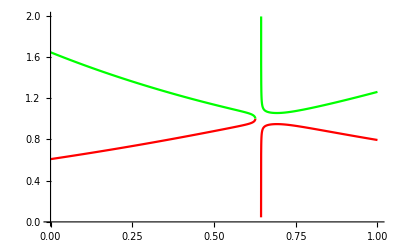

```mathematica
Plot[{e1s @@bain[k,2^(1/6)],e3s @@bain[k,2^(1/6)]},{k,0,1},PlotStyle->{Red,Green}]
```

```mathematica
plusminus1=Table[Show[Plot[{1-f1mu[k,n],f1mu[k,n],Abs[normal[bainnormalp[k,n]]][[1]],Abs[normal[bainnormalp[k,n]]][[2]],Abs[normal[bainnormalp[k,n]]][[3]]},k∈Int2[n],PlotRange->{{0.3,1},{0,1}},MaxRecursion->4,PlotPoints->400, PlotStyle->{{Lighter[Gray],Dashing[Large]},{Lighter[Gray],Dashing[Large]},Orange,Yellow,Red},PlotLabel-> Style[{StringJoin["η=",ToString[NumberForm[n,{5,5}]]],StringJoin["Δ=",ToString[NumberForm[(n^3/Sqrt[2]-1)*100,{5,5}]],"%"]},25],GridLines->{Range[0,1,.1],Range[0,1,.1]}],

Plot[{Abs[normal[bainnormalm[k,n]]][[1]],Abs[normal[bainnormalm[k,n]]][[2]],Abs[normal[bainnormalm[k,n]]][[3]]},k∈Int2[n],PlotRange->{{0.3,1},{0,1}},MaxRecursion->4,PlotPoints->400,PlotStyle->{Lighter[Blue],Cyan,Purple}]],{n,1.12,1.14,.0001}];
Export["plusminus1.mov",plusminus1,ImageSize->1280,Antialiasing->True];
```